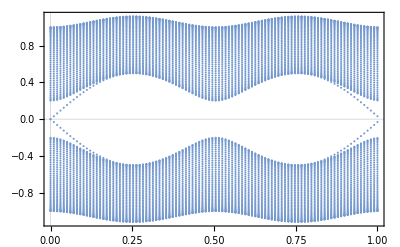

```mathematica
Clear["`*"]
t0=1;
a0=0.2t0;
h0=0.5t0;
num=100;
matH=IdentityMatrix[num];
matE=IdentityMatrix[100];
For[i=1,i≤num,i++,matH[[i,i]]=(-1)^i h0 Sin[2Pi t]];
For[i=1,i≤num-1,i++,matH[[i,i+1]]=1/2(t0+(-1)^i a0 Cos[2Pi t])];
For[i=1,i≤num-1,i++,matH[[i+1,i]]=1/2(t0+(-1)^i a0 Cos[2Pi t])];
For[t=0;i=1,t≤1;i≤100,t=t+0.01;i++,matE[[i]]=Eigenvalues[matH]];
ListPlot[Transpose[matE]/t0,PlotStyle->RGBColor[0.46,0.6,0.81],PlotTheme->"Scientific",DataRange->{0,1},LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
Export["fig.pdf",%]
```

fig.pdf